```mathematica
re
```

```mathematica
ClearAll["Global`*"]
R1=48;

res=out/.NDSolve[{out'[t]==t*R1, out[0]==1},out, {t,0,10}, Method->"ExplicitRungeKutta",MaxStepSize->0.1][[1]];
resNumber=res[2]
```

97.

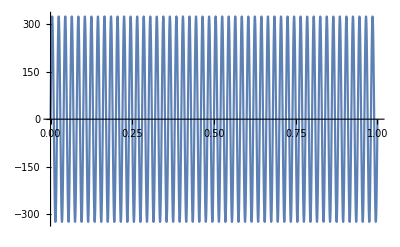

```mathematica
Plot[Sqrt[2]*230*Sin[2*Pi*50*t],{t,0,1}]
```

```mathematica
fce[t_]:=Sqrt[2]*230*Sin[2*Pi*50*t];
fce[5*10^(-3)]
```

230 √2

```mathematica
N[5*10^(-3)]
```

0.005

```mathematica
N[Pi*120/180]
```

2.0944

```mathematica
R1=0.370;
R2=0.225;
L1s=0.00227;
L2s=0.00227;
Lm=0.0825;
L1=0.08477;
L2=0.08477;
pp=2;
intertia=0.4;
sigma=1-Lm^2/(L1*L2);
sigma
```

0.0528396

# MODEL GRAPHICAL TESTING

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
```

## ASM model selected outputs

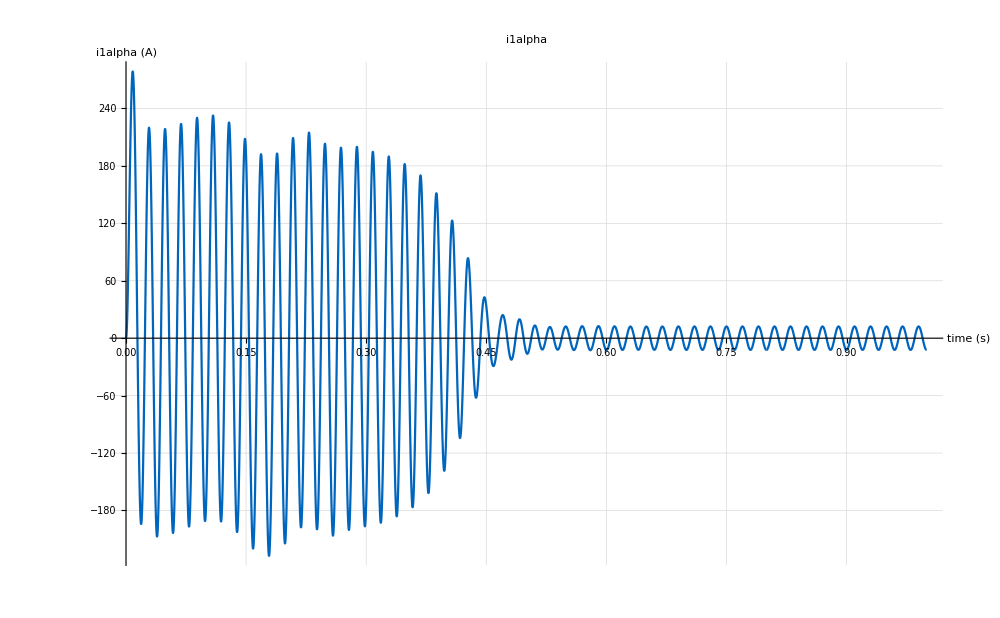

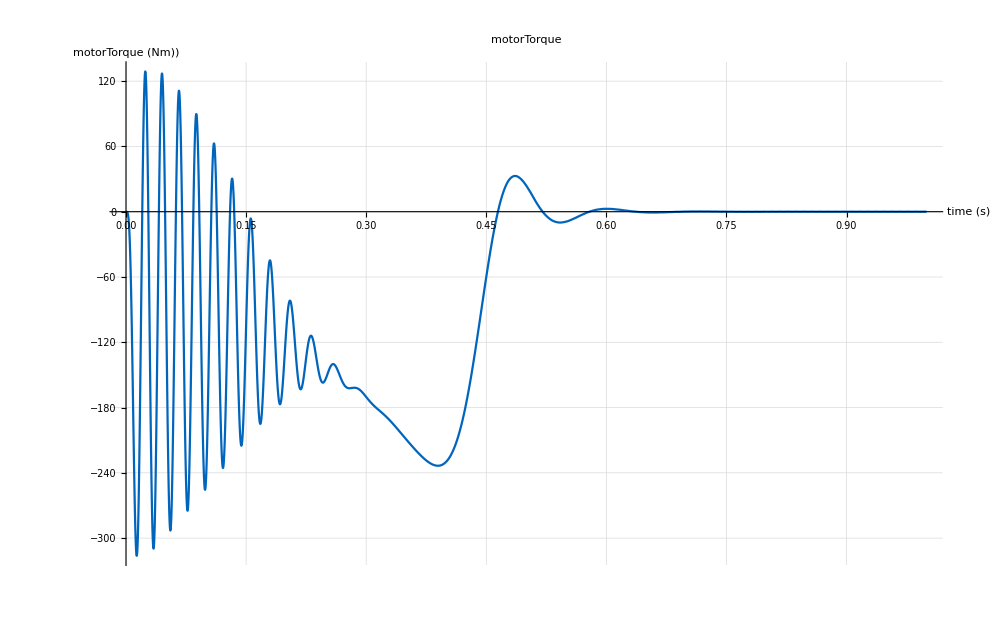

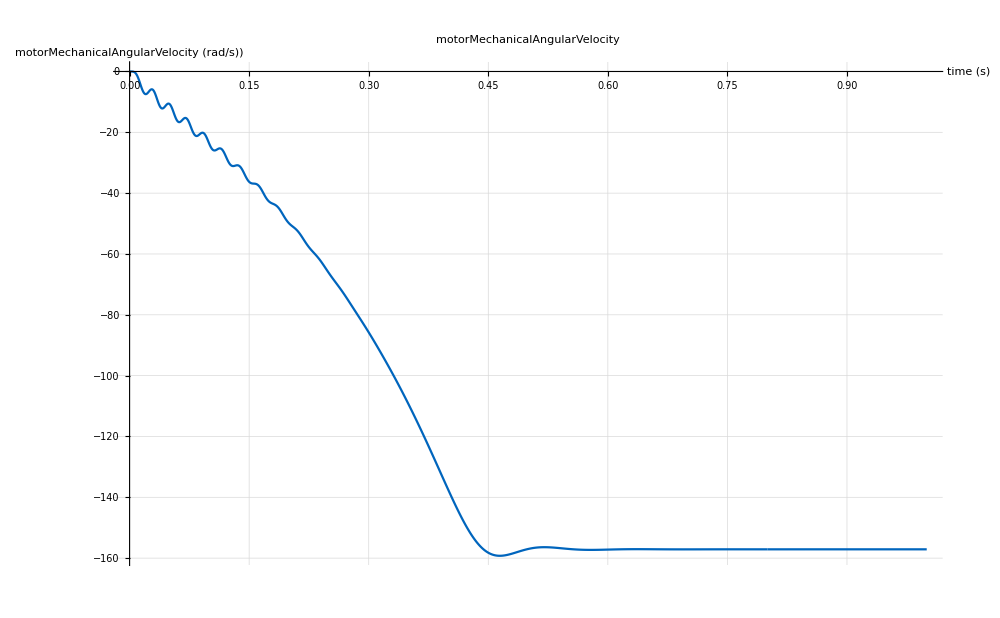

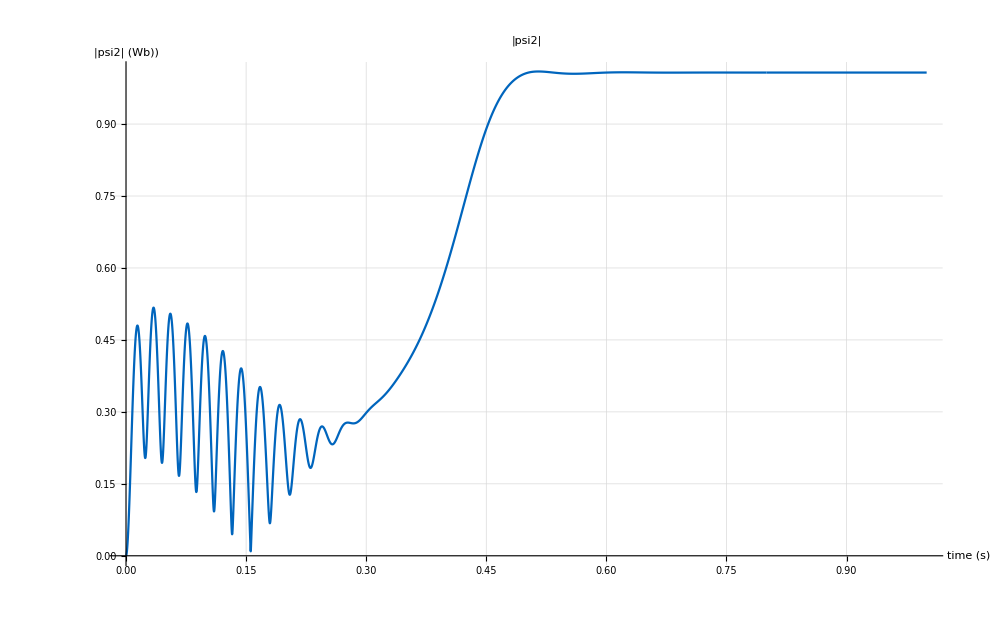

```mathematica
data=Import["./../code/cmodel/outputASM.csv"];
ListPlot[data[[All,1;;2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","i1alpha (A)"},PlotLabel->"i1alpha",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

ListPlot[data[[All,{1,3}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","u1alpha (V)"},PlotLabel->"u1alpha",PlotRangeClipping->False,ImageSize->1000,PlotRange->All];

ListPlot[data[[All,{1,4}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","motorTorque (Nm))"},PlotLabel->"motorTorque",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

ListPlot[data[[All,{1,5}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","motorMechanicalAngularVelocity (rad/s))"},PlotLabel->"motorMechanicalAngularVelocity",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

ListPlot[data[[All,{1,6}]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","|psi2| (Wb))"},PlotLabel->"|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]
```

## ASM current – velocity (I-n) model directly from ASM model values vs values from inverse clark

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
```

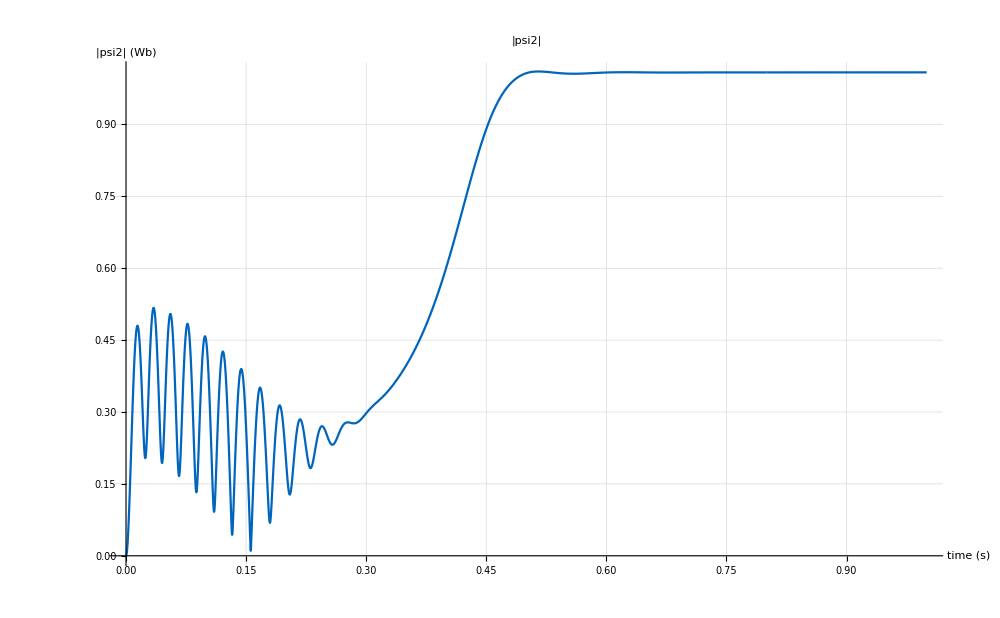

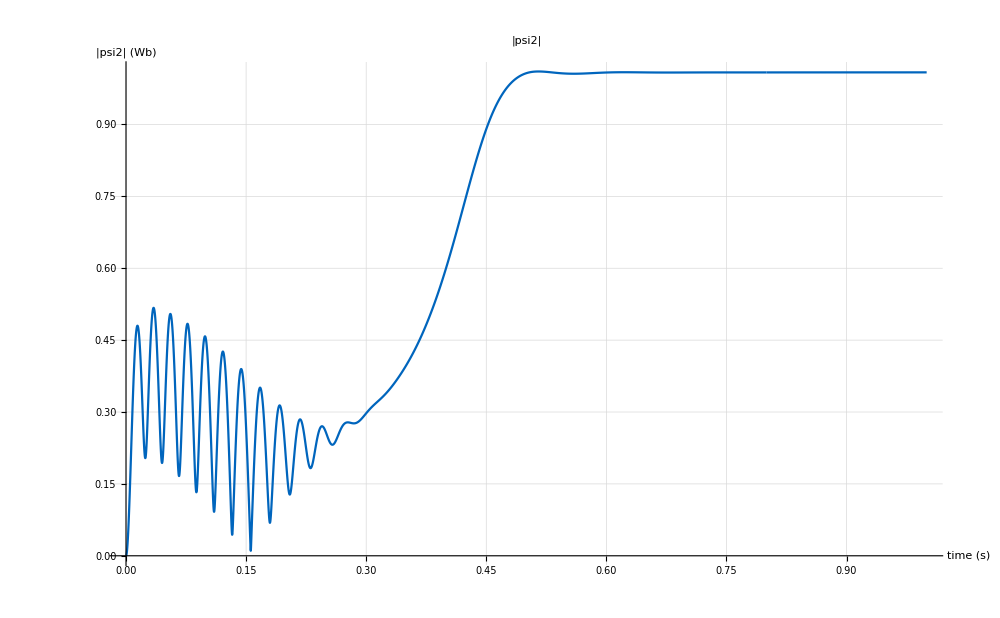

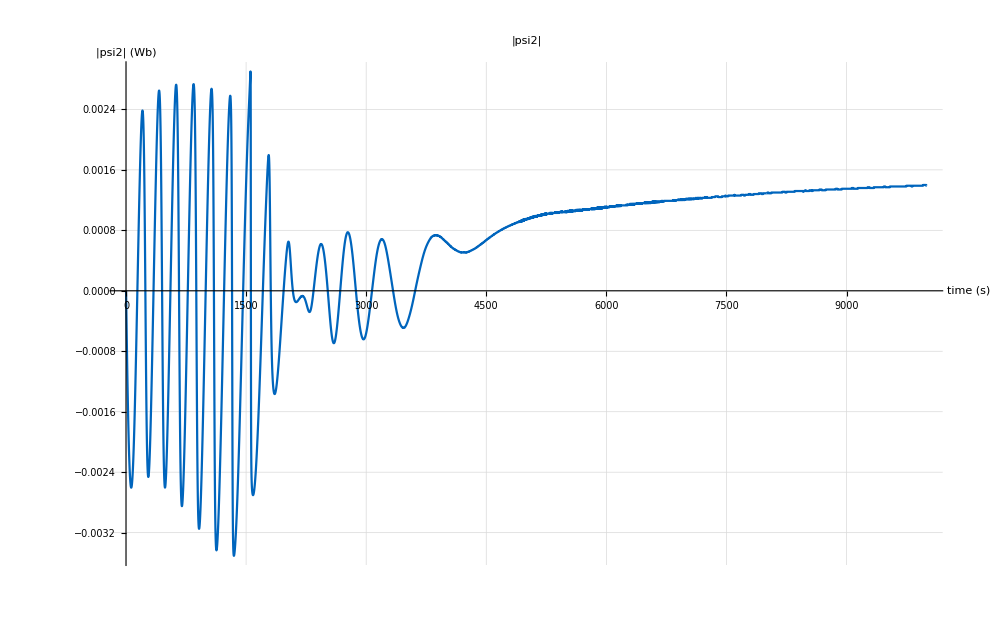

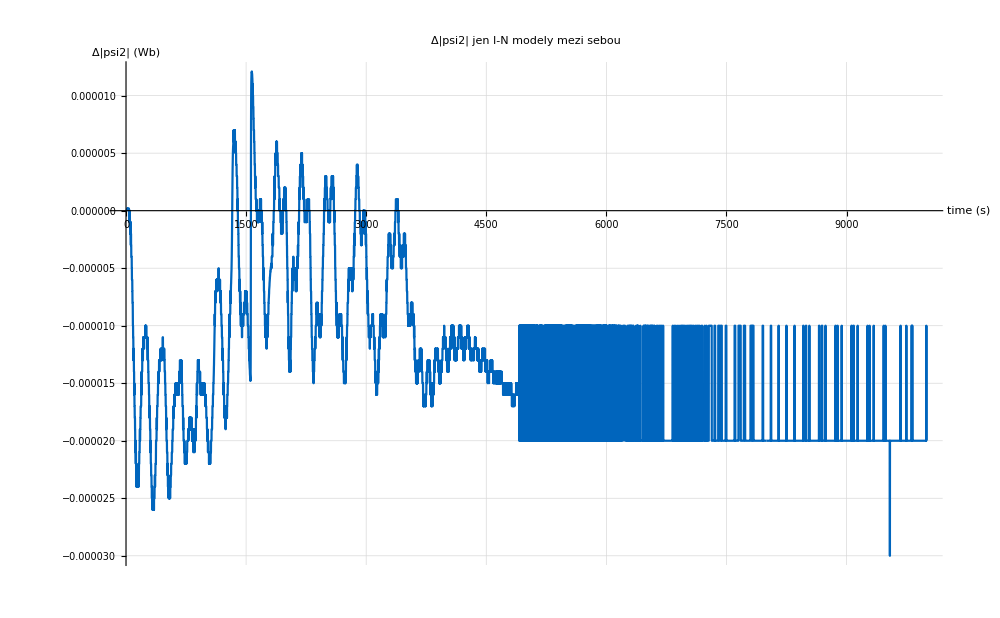

```mathematica
dataCurVel=Import["./../code/cmodel/outputCurVel.csv"];
ListPlot[dataCurVel[[All,1;;2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","|psi2| (Wb)"},PlotLabel->"|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

dataCurVel2=Import["./../code/cmodel/outputCurVel2.csv"];
ListPlot[dataCurVel2[[All,1;;2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","|psi2| (Wb)"},PlotLabel->"|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]


dataASM=Import["./../code/cmodel/outputASM.csv"];
dataCurVel2=Import["./../code/cmodel/outputCurVel2.csv"];
ListPlot[dataCurVel2[[All,2]]-dataASM[[All,6]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","|psi2| (Wb)"},PlotLabel->"|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]

ListPlot[dataCurVel[[All,2]]-dataCurVel2[[All,2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","Δ|psi2| (Wb)"},PlotLabel->"Δ|psi2| jen I-N modely mezi sebou",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]
```

## ASM current – velocity (I-n) model directly from ASM model values vs ASM model internal output

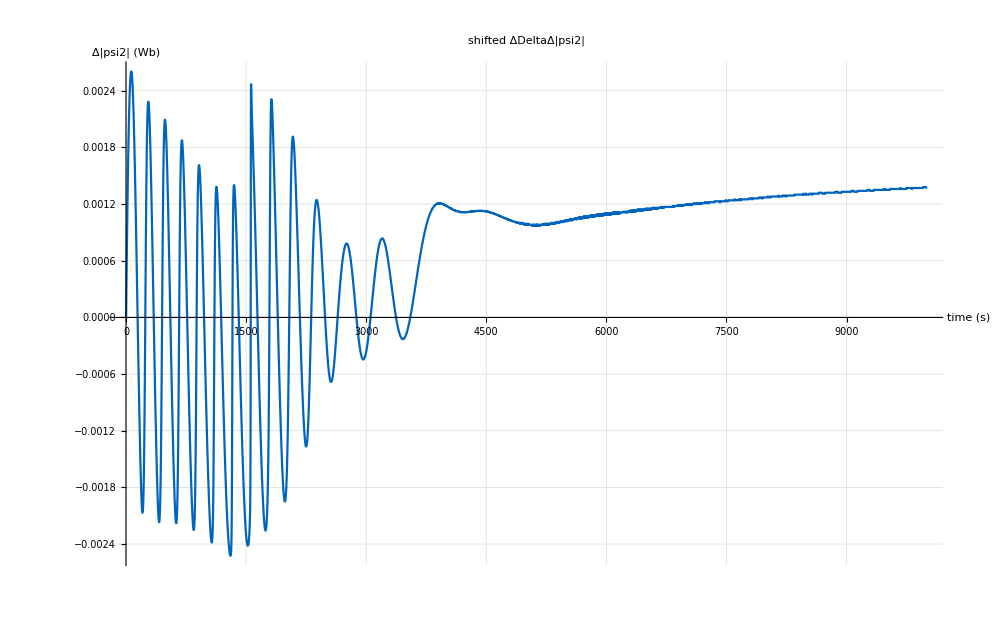

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
dataCurVel=Import["./../code/cmodel/outputCurVel.csv"];
dataASM=Import["./../code/cmodel/outputASM.csv"];
data2=Drop[Prepend[dataASM[[2;;-1,6]],0],-1];
ListPlot[dataCurVel[[2;;-1,2]]-data2,Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","Δ|psi2| (Wb)"},PlotLabel->"shifted ΔDeltaΔ|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]
```

```mathematica
dataCurVel2=Import["~/Downloads/outputCurVel2.csv"];
ListPlot[dataCurVel2[[All,1;;2]],Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","|psi2| (Wb)"},PlotLabel->"|psi2|",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]
```

-Graphics-

```mathematica
Length[dataCurVel[[2;;-1,2]]]
```

10000

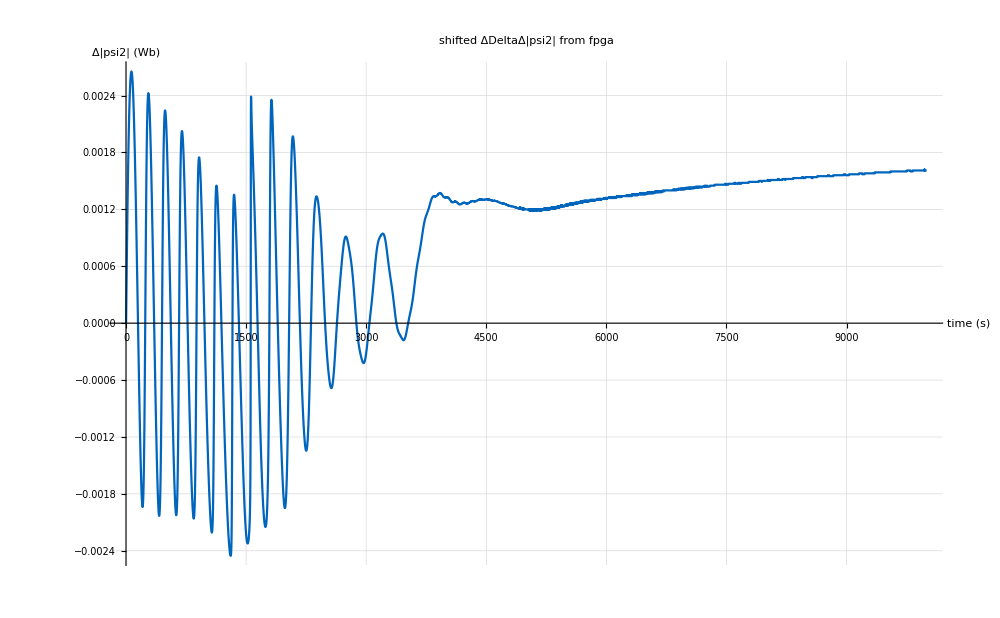

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
dataCurVel2=Import["~/Downloads/outputCurVel2.csv"];
dataASM=Import["./../code/cmodel/outputASM.csv"];
data2=Drop[Prepend[dataASM[[2;;-1,6]],0],-1];
ListPlot[dataCurVel2[[2;;-1,2]]-data2,Joined->True,PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","Δ|psi2| (Wb)"},PlotLabel->"shifted ΔDeltaΔ|psi2| from fpga",PlotRangeClipping->False,ImageSize->1000,PlotRange->All]
```

# TRIANGLE WAVE

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];

ctuBlue=RGBColor["#0065BD"];
ctuLightBlue=RGBColor["#6AADE4"];
ctuRed=RGBColor["#C60C30"];
ctuGreen=RGBColor["#A2AD00"];
ctuGreenyBlue=RGBColor["#00B2A9"];
ctuOrange=RGBColor["#E05206"];
ctuYellow=RGBColor["#F0AB00"];
```

(1)
 |  |  |  |

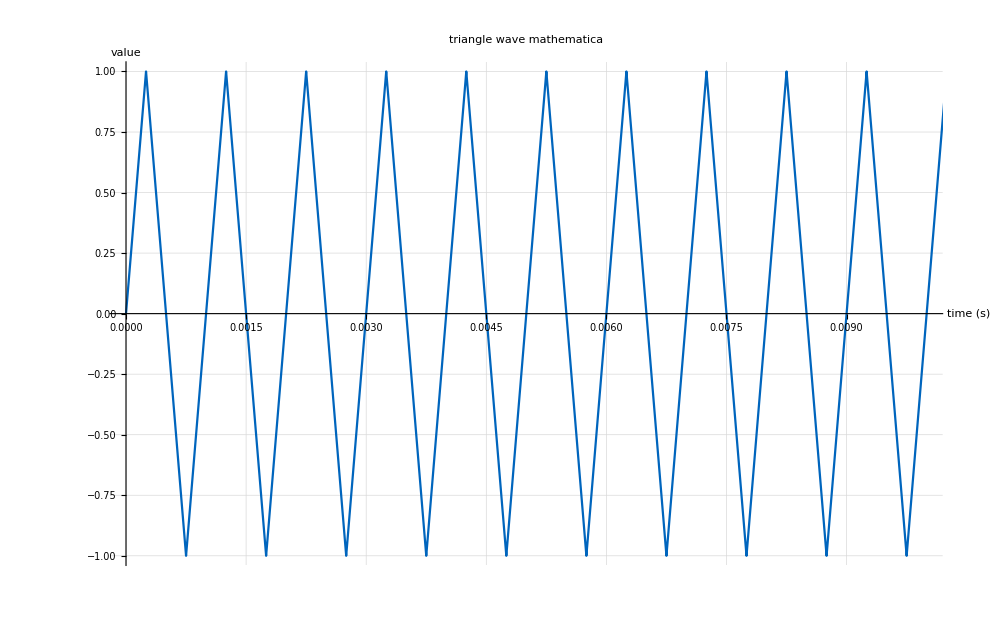

```mathematica
finalCalculationTime=1;
initialCalculationTime=0;
calculationStep=0.00001;
numberOfSteps = (finalCalculationTime - initialCalculationTime)/calculationStep;
triangleWave[t_, amplitude_, period_]:=(4*amplitude)/period*Abs[Mod[(Mod[(t-period/4),period]+period),period]-period/2]-amplitude;

triangleWaveDataMathematica=Table[{t,triangleWave[t,1,0.001]},{t,initialCalculationTime,finalCalculationTime,calculationStep}];



MatrixForm[N[triangleWaveDataMathematica]]

ListPlot[triangleWaveDataMathematica,Joined->True, PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","value"},PlotLabel->"triangle wave mathematica",PlotRangeClipping->False,ImageSize->1000,PlotRange->{{0,0.01},{-1,1}}]
```

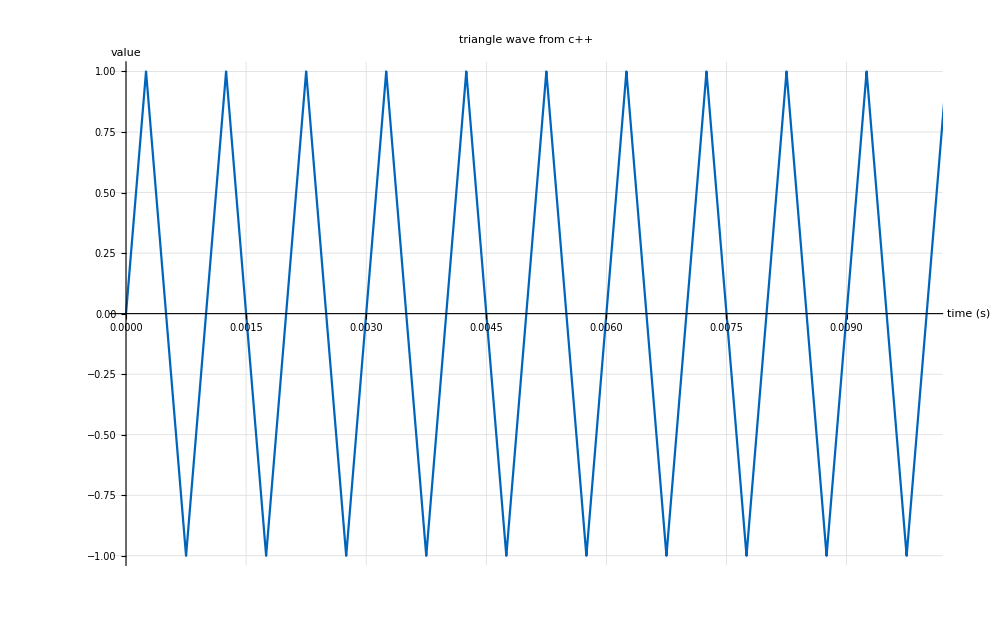

```mathematica
dataTriangleWave=Import["./../code/cmodel/testModules/triangleWaveData.csv"];
MatrixForm[dataTriangleWave];
ListPlot[dataTriangleWave,Joined->True, PlotStyle->ctuBlue,LabelStyle->{FontFamily->"Times New Roman",15,Black, Bold},AxesOrigin->{0,0},GridLines->Automatic,AxesLabel->{"time (s)","value"},PlotLabel->"triangle wave from c++",PlotRangeClipping->False,ImageSize->1000,PlotRange->{{0,0.01},{-1,1}}]
```

```mathematica
Mod[5,3.55]
```

1.45